# Planar3D v3.1.0

```mathematica
ClearAll[folder,parameters,size,middle,cellLength,showAllBarriers,textPadding,ticks,barriers,concentration,fracture,opening,pressure,openingFilenames,openingAtCheckStep,numberOfCheckSteps];
```

## Построение сеточных графиков в 2D

Указываем путь до папки с входными данными

```mathematica
folder="G:\\actualplanar\\planar5_11\\Planar3D\\Sources\\Results\\";
If[!FileExistsQ[folder], Print[Style["Папка не существует!",{Red,FontSize->24}]]]
```

Считываем параметры расчёта

```mathematica
parameters=Import[folder<>"parameters.json","RawJSON"];
(*height=parameters["mesh"]["height"];
length=parameters["mesh"]["length"];
middleH = Floor[0.5*height]+1;
middleL=Floor[0.5*length]+1;*)
size=parameters["mesh"]["height"];
middle=Floor[0.5*size]+1;
cellLength= parameters["mesh"]["cell"]["length"];
```

Задаём параметры отображения

```mathematica
(*Если True, на графике будут выводиться границы слоёв,расположенных за пределами расчётной области*)
showAllBarriers=False;
textPadding=2;
```

Указываем риски по осям графика

```mathematica
(*ticksSetVertical={
{1,N[-cellLength*(middleH-0.5)]},
{1+Floor[height/4],N[-cellLength*(middleH-0.5)*0.5]},
{1+Floor[height/2],0},
{1+Floor[3height/4],N[cellLength*(middleH-0.5)*0.5]},
{height,N[cellLength*(middleH-0.5)]}
};
ticksSetHorizontal={
{1,N[-cellLength*(middleL-0.5)]},
{1+Floor[length/4],N[-cellLength*(middleL-0.5)*0.5]},
{1+Floor[length/2],0},
{1+Floor[3length/4],N[cellLength*(middleL-0.5)*0.5]},
{length,N[cellLength*(middleL-0.5)]}
};*)
ticksSet={
{1,N[-cellLength*(middle-0.5)]},
{1+Floor[size/4],N[-cellLength*(middle-0.5)*0.5]},
{1+Floor[size/2],0},
{1+Floor[3size/4],N[cellLength*(middle-0.5)*0.5]},
{size,N[cellLength*(middle-0.5)]}
};
ticks={{ticksSet,None},{ticksSet,None}};
(*ticks={{ticksSetHorizontal,None},{ticksSetVertical,None}};*)
```

По рискам намечаем линии сетки

```mathematica
lines={};
For[
i=1;AppendTo[lines,{}];leftTicks=ticks[[1]][[1]],
i≤ Length[leftTicks],
++i,
AppendTo[lines[[Length[lines]]],leftTicks[[i]][[1]]-0.5]
]
For[
i=1;AppendTo[lines,{}];rightTicks=ticks[[1]][[1]],
i≤ Length[rightTicks],
++i,
AppendTo[lines[[Length[lines]]],rightTicks[[i]][[1]]-0.5]
]
```

Создаём массив линий–границ слоёв пласта

```mathematica
lineBarriers={};
nominalStress=0.;
For[
i=1; layers=parameters["layers"],
i<=Length[layers],
++i,
If[0>layers[ToString[i]]["y1"]*layers[ToString[i]]["y2"],nominalStress=layers[ToString[i]]["stress"]]
]
For[
i=1; layers=parameters["layers"],
i<=Length[layers],
++i,
barrierCoordinate=middle-Round[layers[ToString[i]]["y1"]/cellLength+0.5];
If[showAllBarriers||1≤barrierCoordinate && size≥barrierCoordinate,
AppendTo[lineBarriers,Line[{{1,barrierCoordinate},{size,barrierCoordinate}}]];
If[barrierCoordinate<middle ,
stress=layers[ToString[i-1]]["stress"],
stress=layers[ToString[i]]["stress"]
];
stress-=nominalStress;
stress/=10^6;
signum="";
If[stress > 0, signum="+"];
AppendTo[lineBarriers,Text[signum<>ToString[N[stress]]<>" МПа",{2+textPadding,textPadding+barrierCoordinate}]]
]
]
barriers=Graphics[lineBarriers];
```

Задаём функции для построения трещины и цветовую гамму

```mathematica
(*myRainbow=Function[x,Blend[{LightBlue,Green,LightGreen,White,Yellow,Orange,
RGBColor[0.6,0,0]},x]];*)
myRainbow=Function[x,Blend[{White,White,White,White,White,RGBColor[0.6,0.6,0.6],Yellow,Orange,RGBColor[0.6,0,0]},x]];
(*myRainbow=Function[x,If[0.5>x,White,ColorData["Rainbow",x]]];*)
myRainbow3D=Function[{x,y,z},ColorData["Rainbow",z]];
GlueMatrix=Function[{matrix},Transpose[Join[TakeList[Reverse[Transpose[matrix]],{Length[matrix[[1]]]-1}][[1]],Transpose[matrix]]]];
PlotMatrix= Function[{matrix,matrixName},
Show[
MatrixPlot[
GlueMatrix[matrix],PlotLabel->matrixName, FrameTicks->ticks,GridLines->lines,ColorFunction->myRainbow,PlotTheme->"Business",PlotLegends->Automatic,ImageSize->Large],
barriers]
];
```

Задаём функцию для построения графика характеристики трещины

```mathematica
plotCharacteristic=Function[{index,valueName},ListLinePlot[Table[{fracture[[i]][[1]],fracture[[i]][[index]]},{i,2,Length[fracture],1}],PlotRange->All,AxesLabel->{"Время, мин",valueName}]];
```

Задаём функцию для карты слоёв

```mathematica
plotLayersMap=Function[stressLine={};
plainModulusLine={};
carterLine={};
minY=100000;
maxY=-100000;
layers=parameters["layers"];
For[
i=0,
i< Length[layers],
++i,
y1=layers[ToString[i]]["y1"];
y2=layers[ToString[i]]["y2"];
plainModulus=N[layers[ToString[i]]["Young's modulus"]*10^-9/(1-Power[layers[ToString[i]]["Poisson's ratio"],2])];
AppendTo[stressLine,{N[layers[ToString[i]]["stress"]*10^-6],y1}];
AppendTo[stressLine,{N[layers[ToString[i]]["stress"]*10^-6],y2}];
AppendTo[plainModulusLine,{plainModulus,y1}];
AppendTo[plainModulusLine,{plainModulus,y2}];
AppendTo[carterLine,{N[layers[ToString[i]]["Carter's coefficient"]*10^6],y1}];
AppendTo[carterLine,{N[layers[ToString[i]]["Carter's coefficient"]*10^6],y2}];
minY=Min[{y1,y2,minY}];
maxY=Max[{y1,y2,maxY}];
];
plotStyles={{Red,Dotted},{Green,Dashed},{Purple,Dotted}};
plotLegend=Placed[LineLegend[{"Напряжения","Плоский модуль Юнга","Коэффициент Картера"},LegendLabel->"Карта слоёв", LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],Right];
commonPlotParameters={ImageSize->{Tiny,Medium},AspectRatio->Full,AxesStyle->Transparent,PlotRange->{All,{minY,maxY}},Frame->{False,True,False,False}};
stressLinePlot=ListLinePlot[{stressLine,{None},{None}},PlotStyle->plotStyles,PlotLegends->plotLegend,commonPlotParameters];
plainModulusLinePlot=ListLinePlot[plainModulusLine,PlotStyle->plotStyles[[2]],commonPlotParameters];
carterLinePlot=ListLinePlot[carterLine,PlotStyle->plotStyles[[3]],commonPlotParameters];
Overlay[{stressLinePlot,plainModulusLinePlot,carterLinePlot}]];
```

Загружаем данные для построения

```mathematica
concentration=Import[folder<>"concentration_m.txt", "Table"];
fracture=Import[folder<>"fracture_m.txt", "Table"];
opening=Import[folder<>"opening_m.txt", "Table"];
pressure=Import[folder<>"pressure_m.txt", "Table"];
```

```mathematica
openingFilenames=FileNames["*_m.txt",folder<>"Opening/"];
openingAtCheckStep=Function[t,Import[openingFilenames[[t]], "Table"]];
numberOfCheckSteps=Length[openingFilenames];
```

Выводим время последнего запуска

```mathematica
If[!FileExistsQ[folder], Print[Style["Папка не существует!",{Red,FontSize->24}]]]
Print[Style["Время последнего запуска:" Style[DateString[],Orange],{FontSize->24}]]
```

Время последнего запуска: Mon 12 Nov 2018 14:22:43

Строим графики

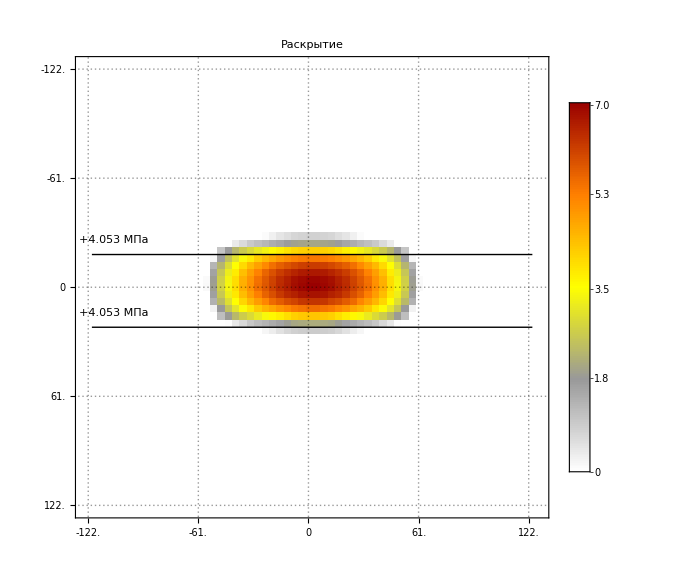

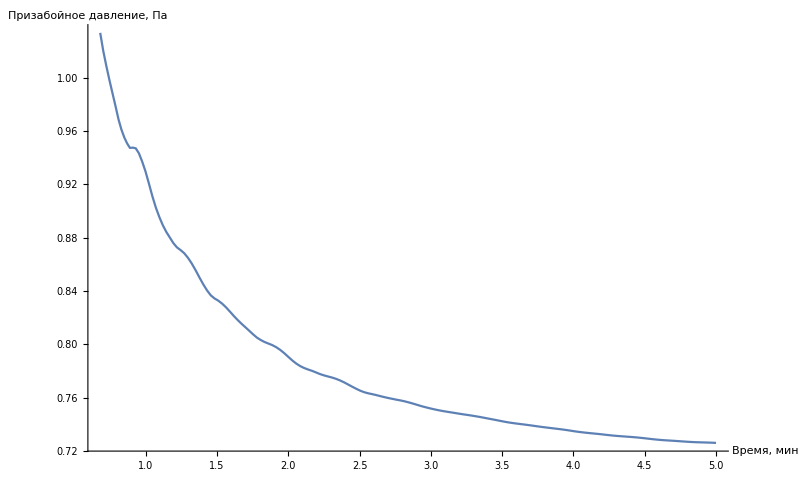

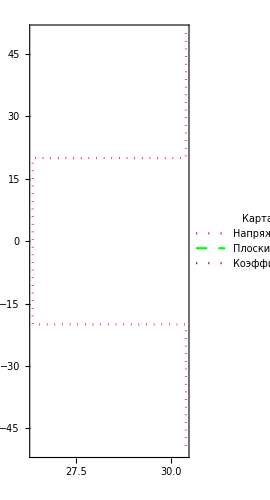
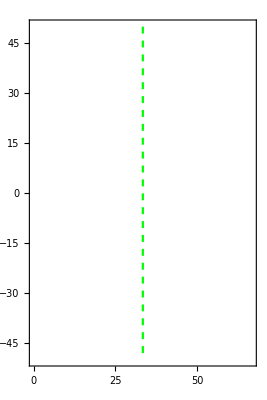
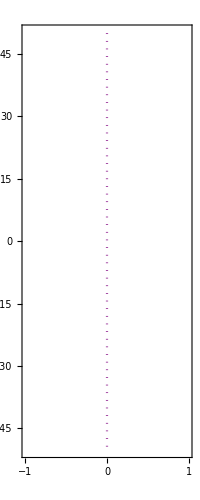

```mathematica
PlotMatrix[opening, "Раскрытие"]
plotCharacteristic[3,"Призабойное давление, Па"]
If[0<Max[concentration],PlotMatrix[concentration, "Концентрация проппанта"]]
plotLayersMap[]
```

Создаём GIF-анимацию

```mathematica
iterationStep=40;
plotName="Раскрытие";
plotDataList=Table[openingAtCheckStep[i],{i,1,numberOfCheckSteps,iterationStep}];
plotList=Table[
PlotMatrix[plotDataList[[i]],plotName<>" на шаге проверки №"<>ToString[1+(i-1)*iterationStep]],
{i,1,Length[plotDataList],1}
];
Export["~/Desktop/opening.gif",plotList]
```

Export::nodir: Directory C:\Users\Nikita\Documents\~\Desktop\ does not exist.

Export::noopen: Cannot open ~/Desktop/opening.gif.

$Failed

Экспериментальная секция!

```mathematica
openingDouble={};
For[
i=1,
i<Length[opening],
++i,

AppendTo[openingDouble,{}];
For[
j=1,
j<Length[opening[[middle]]],
++j,
AppendTo[openingDouble[[2*(i-1)+1]],opening[[i]][[j]]];
AppendTo[openingDouble[[2*(i-1)+1]],0.5*(opening[[i]][[j]]+opening[[i]][[j+1]])]
];
AppendTo[openingDouble[[2*(i-1)+1]],opening[[i]][[Length[opening[[i]]]]]];

AppendTo[openingDouble,{}];
For[
j=1,
j<Length[opening[[middle]]],
++j,
AppendTo[openingDouble[[2*(i-1)+2]],0.5*(opening[[i]][[j]]+opening[[i+1]][[j]])];
AppendTo[openingDouble[[2*(i-1)+2]],0.5*(opening[[i]][[j]]+opening[[i+1]][[j+1]])]
];
AppendTo[openingDouble[[2*(i-1)+2]],opening[[i]][[Length[opening[[i]]]]]];
]
```

```mathematica
fracture
```

{{Time,[min],Opening,[mm],Pressure,[Pa],Length,[m],Height,[m],Aspect,raio,[n/d]},{0.67987,4.79576,1.03373,36.3535,36.3535,1},{0.701277,4.80584,1.02017,36.7402,39.6614,0.926348},{0.722683,4.81042,1.00895,37.1294,39.9368,0.929703},{0.744714,4.81381,0.998219,37.5244,40.2357,0.932616},{0.766589,4.8198,0.988165,37.9086,40.5274,0.935382},{0.787995,4.82813,0.978386,38.2757,40.8062,0.937988},{0.808777,4.84135,0.968587,38.6253,41.076,0.940337},{0.829089,4.86479,0.96099,38.9648,41.3425,0.942488},{0.849089,4.89479,0.955157,39.2978,41.6089,0.944457},{0.868933,4.9295,0.950682,39.6287,41.8791,0.946264},{0.88862,4.96668,0.947339,39.9586,42.1536,0.94793},{0.908464,5.00654,0.94759,40.2926,42.4358,0.949496},{0.929402,5.03301,0.947047,40.6426,42.7354,0.951029},{0.951277,5.04395,0.94335,42.8333,43.0461,0.995057},{0.973933,5.04401,0.937225,43.178,43.3641,0.995709},{0.99737,5.03861,0.929786,43.5364,43.6886,0.996516},{1.02143,5.03044,0.920686,43.9043,44.017,0.99744},{1.04581,5.02697,0.911089,44.2773,44.3462,0.998446},{1.07034,5.03257,0.902539,44.653,44.3793,1.00617},{1.09503,5.04642,0.895385,45.031,44.5987,1.00969},{1.11956,5.06559,0.889222,45.4068,44.8151,1.0132},{1.14409,5.08976,0.884198,45.7846,45.032,1.01671},{1.16878,5.11616,0.880016,46.167,45.253,1.0202},{1.19362,5.14317,0.875815,46.5531,45.4791,1.02362},{1.21846,5.17264,0.872679,46.9393,45.7084,1.02693},{1.24393,5.20187,0.87066,47.329,45.9455,1.03011},{1.26971,5.22475,0.868264,47.7146,46.1846,1.03313},{1.29581,5.24127,0.864828,48.095,46.423,1.03602},{1.32237,5.25369,0.860555,48.4731,46.6603,1.03885},{1.3494,5.26398,0.855479,48.8507,46.8961,1.04168},{1.37659,5.27526,0.85001,51.0727,47.1279,1.0837},{1.40362,5.29019,0.844827,51.415,47.3545,1.08575},{1.42987,5.30901,0.840322,51.7578,47.5724,1.08798},{1.45565,5.33191,0.836706,52.1054,47.7855,1.0904},{1.48128,5.3582,0.834416,52.4608,47.9969,1.093},{1.508,5.38426,0.832714,52.8391,48.2166,1.09587},{1.53534,5.40634,0.830463,53.2317,46.4315,1.14646},{1.563,5.42521,0.82765,53.6337,46.5985,1.15098},{1.59034,5.44186,0.824449,54.0356,46.7547,1.15573},{1.61737,5.45839,0.821185,54.434,46.9033,1.16056},{1.64425,5.47574,0.818184,54.8261,47.0464,1.16536},{1.67143,5.49413,0.815368,55.2152,47.1873,1.17013},{1.69862,5.51295,0.812728,55.5956,47.3251,1.17476},{1.72518,5.53142,0.810135,55.9607,47.4577,1.17917},{1.75159,5.55022,0.807502,56.3198,47.5881,1.18349},{1.77815,5.57083,0.805072,56.6801,47.7184,1.1878},{1.80456,5.59317,0.803264,58.727,47.8475,1.22738},{1.83112,5.61581,0.801768,59.0528,47.9771,1.23085},{1.858,5.63815,0.800584,59.3939,48.1079,1.2346},{1.88581,5.65885,0.799407,59.7582,48.2429,1.23869},{1.91409,5.67635,0.797818,60.1384,48.3795,1.24306},{1.94284,5.69121,0.795746,60.5328,48.5171,1.24766},{1.97175,5.70433,0.793229,60.9357,48.6537,1.25244},{2.00018,5.71706,0.790452,61.3385,48.7859,1.2573},{2.02815,5.73128,0.78777,61.7409,48.9134,1.26225},{2.05565,5.74778,0.785455,62.139,49.0363,1.2672},{2.083,5.7666,0.783587,62.5328,49.1562,1.27212},{2.11034,5.78714,0.782166,62.9215,49.2743,1.27697},{2.13768,5.80825,0.781047,63.3037,49.3908,1.28169},{2.16518,5.82901,0.780061,63.6831,49.5071,1.28634},{2.19253,5.84839,0.778904,64.0575,49.622,1.29091},{2.21987,5.8674,0.77768,64.4311,49.7364,1.29545},{2.24737,5.88689,0.776704,64.8063,49.8507,1.30001},{2.2755,5.90633,0.775869,66.9073,49.967,1.33903},{2.30425,5.92492,0.775062,67.2638,50.0852,1.34299},{2.33346,5.94176,0.774062,67.6354,50.2045,1.3472},{2.363,5.95687,0.7728,68.02,50.3242,1.35164},{2.39221,5.97052,0.77131,68.4084,50.4416,1.35619},{2.42096,5.98349,0.769669,68.798,50.5558,1.36083},{2.44956,5.99689,0.768024,69.1929,50.6681,1.36561},{2.478,6.01117,0.766455,69.5925,50.7785,1.37051},{2.50581,6.02639,0.765046,69.9886,50.885,1.37543},{2.53331,6.04301,0.76396,70.3814,50.9893,1.38032},{2.56065,6.06047,0.763156,70.768,51.092,1.38511},{2.58815,6.07819,0.762533,71.1498,51.1942,1.3898},{2.61565,6.09516,0.761863,71.5261,51.2955,1.39439},{2.64315,6.1115,0.761091,71.8992,51.3962,1.39892},{2.67081,6.1279,0.760359,72.2724,51.4969,1.40343},{2.69925,6.14464,0.759669,72.6535,51.5999,1.40802},{2.72831,6.1615,0.759027,74.7079,51.7046,1.4449},{2.75784,6.17809,0.758389,75.0603,51.8106,1.44874},{2.78768,6.19426,0.75779,75.4266,51.9175,1.45282},{2.81768,6.20937,0.75709,75.8053,52.0246,1.45711},{2.84721,6.22327,0.756256,76.1882,52.1296,1.46151},{2.87675,6.23676,0.755363,76.5801,52.2343,1.46609},{2.90628,6.25001,0.754408,76.9805,52.3384,1.47082},{2.93534,6.26327,0.753469,77.3819,52.4404,1.47562},{2.96378,6.27681,0.752668,77.7801,52.5396,1.48041},{2.9919,6.29036,0.751922,78.1753,52.6373,1.48517},{3.02003,6.30411,0.75122,78.5677,52.7345,1.48987},{3.04831,6.31815,0.750576,78.9572,52.8317,1.4945},{3.07659,6.33233,0.749992,79.3413,52.9284,1.49903},{3.10503,6.34667,0.749467,79.723,53.025,1.5035},{3.13409,6.36123,0.748973,80.1085,53.1233,1.50797},{3.16378,6.3758,0.748471,80.4983,53.2235,1.51246},{3.19409,6.39028,0.747935,80.8935,53.3256,1.51697},{3.22471,6.40472,0.747415,82.9883,53.4286,1.55326},{3.2555,6.41901,0.746939,83.3518,53.5321,1.55704},{3.28612,6.43267,0.746437,83.7246,53.6352,1.561},{3.31675,6.44585,0.745898,84.1083,53.7383,1.56515},{3.34737,6.45861,0.745335,84.5021,53.8415,1.56946},{3.37768,6.47076,0.744713,84.9008,53.9437,1.57388},{3.40737,6.48259,0.744099,85.2987,54.0437,1.57833},{3.43659,6.49419,0.743513,85.6959,54.1422,1.58279},{3.46565,6.50556,0.742907,86.0924,54.2401,1.58725},{3.49456,6.51686,0.74229,86.4846,54.3374,1.59162},{3.52378,6.5285,0.741689,86.8769,54.4359,1.59595},{3.55315,6.54063,0.741168,87.2658,54.5349,1.60018},{3.58284,6.55307,0.740711,87.6536,54.635,1.60435},{3.61331,6.56586,0.740285,88.046,54.7379,1.6085},{3.64425,6.57869,0.739875,88.4396,54.8425,1.61261},{3.67565,6.59135,0.739437,88.836,54.949,1.6167},{3.70737,6.60388,0.738977,90.8991,55.0568,1.651},{3.73925,6.61621,0.738491,91.2651,55.1654,1.65439},{3.77081,6.62838,0.738017,91.6398,55.2731,1.65795},{3.80253,6.64067,0.73759,92.0282,55.3816,1.66171},{3.83425,6.65275,0.737169,92.4272,55.4903,1.66564},{3.86565,6.66459,0.736764,92.8311,55.5982,1.66968},{3.89643,6.67597,0.736375,93.2339,55.7042,1.67373},{3.92675,6.6868,0.735957,93.6355,55.8088,1.67779},{3.95675,6.69724,0.735502,94.0361,54.9185,1.71228},{3.98659,6.70741,0.735008,94.4332,55.0049,1.71681},{4.01675,6.71787,0.734511,94.828,55.093,1.72124},{4.04737,6.72885,0.734074,95.2218,55.1831,1.72556},{4.07831,6.74012,0.733685,95.613,55.2748,1.72978},{4.10987,6.75172,0.733329,96.0056,55.3688,1.73393},{4.14206,6.7635,0.732995,96.4002,55.4653,1.73803},{4.17471,6.7752,0.732648,96.797,55.5636,1.74209},{4.20768,6.7867,0.732263,98.8567,55.6633,1.77598},{4.24034,6.79798,0.731859,99.2148,55.7625,1.77924},{4.27331,6.80956,0.731485,99.5891,55.8629,1.78274},{4.30643,6.82135,0.731171,99.9777,55.964,1.78647},{4.33956,6.83315,0.730895,100.378,56.0652,1.79037},{4.37206,6.84459,0.73065,100.779,56.1648,1.79434},{4.40393,6.85551,0.730403,101.179,55.2707,1.8306},{4.43534,6.86587,0.730128,101.577,55.3487,1.83522},{4.46643,6.87576,0.72981,101.975,55.4267,1.83983},{4.49721,6.88527,0.729452,102.369,55.5044,1.84435},{4.52831,6.89484,0.729062,102.763,55.5833,1.8488},{4.55971,6.90469,0.728687,103.155,55.6633,1.8532},{4.59159,6.91496,0.728341,103.547,55.7447,1.85752},{4.62409,6.92576,0.728049,103.939,55.8277,1.86179},{4.65721,6.93696,0.727809,104.334,55.9124,1.86602},{4.69081,6.94827,0.727587,104.729,55.9982,1.87023},{4.72471,6.95949,0.727352,106.761,56.0847,1.90356},{4.75878,6.97062,0.727096,107.121,56.1713,1.90704},{4.79284,6.98176,0.726843,107.494,56.2577,1.91073},{4.82675,6.99302,0.726622,107.878,56.3434,1.91464},{4.86081,7.00454,0.726457,108.275,56.4291,1.91878},{4.89456,7.01599,0.726344,108.679,56.5137,1.92306},{4.92768,7.02704,0.726243,109.083,56.5963,1.92739},{4.96034,7.03761,0.726129,109.486,56.6774,1.93174},{4.99253,7.04764,0.725984,109.887,56.7569,1.9361},{5.00003,7.04988,0.725945,109.979,56.775,1.93711}}